```mathematica
Clear[VV,Vpp]
VV[phi_] = beta*H^2 *vev^2(1/(beta* epsilon^2)- phi^2/2-b/3*(phi)^3+1/4*(phi)^4);
Vpp[phi_] =D[VV[phi],{phi,2}]/vev^2
logRules ={Log[x_ y_]:>Log[x]+Log[y],Log[x_^k_]:>k*Log[x]};
paramRules={H->1,beta->45,b->1/4,epsilon->46/1000,μ->1,vev->1};
```

beta H^2 (-1-2 b phi+3 phi^2)

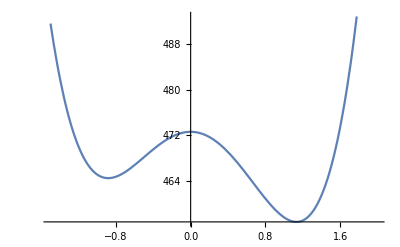

```mathematica
Plot[VV[phi]/.paramRules,{phi,-1.5,2}]
```

```mathematica
phiFalse = phi/.Solve[D[VV[phi],phi]==0,phi][[2]]
```

1/2 (b-√(4+b^2))

```mathematica
phiFalse/.paramRules//N
```

-0.882782

```mathematica
Simplify[Vpp[phiFalse],Assumptions->{b∈Reals}]
```

1/2 (4+b^2-b √(4+b^2)) beta H^2

```mathematica
(* Neglecting curvature terms  *)
```

```mathematica
flucOp =k4^2 +(* Csc[chi]^2 *)k^2+Vproxy;
flucOpDiscrete =k4^2 +(* Csc[chi]^2 *)ell(ell+2)+Vproxy;
```

```mathematica
CWplanar = 1/2*4Pi/(2Pi)^4 (Integrate[k^2(Log[flucOp]-Log[flucOp/.{Vproxy->Vfalse}]),{k,0,Λ},{k4,-Infinity,Infinity},Assumptions->{Vproxy>0,Vfalse>0,Λ>0}])/.{}
```

(-2 Λ √(Vfalse+Λ^2) (Vfalse+2 Λ^2)+2 Λ √(Vproxy+Λ^2) (Vproxy+2 Λ^2)-Vfalse^2 (Log[Vfalse]-2 Log[Λ+√(Vfalse+Λ^2)])+Vproxy^2 (Log[Vproxy]-2 Log[Λ+√(Vproxy+Λ^2)]))/(64 π^2)

```mathematica
greenHom= 1/2/(2Pi)  (Integrate[(Log[flucOpDiscrete]),{k4,-Λ4,Λ4},Assumptions->{Vproxy>0,Vfalse>0,ell>0,Λ4>0}])/.{}
```

(4 √(ell (2+ell)+Vproxy) ArcTan[Λ4/(√(ell (2+ell)+Vproxy))]+2 Λ4 (-2+Log[ell (2+ell)+Vproxy+Λ4^2]))/(4 π)

```mathematica
CWplanarPerEll = 1/2/(2Pi)  (Integrate[(Log[flucOpDiscrete]-Log[flucOpDiscrete/.{Vproxy->Vfalse}]),{k4,-Infinity,Infinity},Assumptions->{Vproxy>0,Vfalse>0,ell>0}])/.{}
```

1/2 (-√(ell (2+ell)+Vfalse)+√(ell (2+ell)+Vproxy))

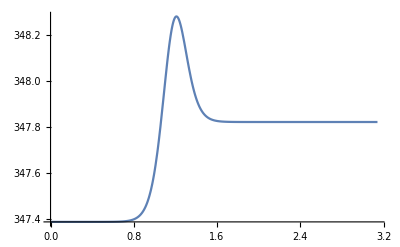

```mathematica
Plot[Evaluate[2Pi*√(ell (2+ell)+Vproxy)//.Join[{Vproxy->VV[bounceLoad[chi]],Vfalse->VV[phiFalse],ell->50},paramRules]],{chi,0,Pi},PlotRange->{Automatic,Full}]
```

```mathematica
largeEllExp=Normal@Series[CWplanarPerEll,{ell,Infinity,4}]/.{ell->Lplus1-1}
```

(Vfalse-Vproxy)/(4 (-1+Lplus1)^2)+(-Vfalse+Vproxy)/(4 (-1+Lplus1))+(-6 Vfalse+Vfalse^2+6 Vproxy-Vproxy^2)/(16 (-1+Lplus1)^3)+(10 Vfalse-3 Vfalse^2-10 Vproxy+3 Vproxy^2)/(16 (-1+Lplus1)^4)

```mathematica
(* Included the factors coming from integration of the angles in the trace --- (ell+1)^2*)
```

```mathematica
CWplanarPerEllSummed=Normal@Series[Sum[(Lplus1)^2largeEllExp,{Lplus1,2,Lplus1Max}],{Lplus1Max,Infinity,0}]/.{Lplus1Max->Λ+1}
```

1/8 (-Vfalse+Vproxy) (1+Λ)+1/8 (-Vfalse+Vproxy) (1+Λ)^2+1/1440(360 Vfalse-180 EulerGamma Vfalse+30 π^2 Vfalse+10 π^4 Vfalse+90 EulerGamma Vfalse^2-15 π^2 Vfalse^2-3 π^4 Vfalse^2-360 Vproxy+180 EulerGamma Vproxy-30 π^2 Vproxy-10 π^4 Vproxy-90 EulerGamma Vproxy^2+15 π^2 Vproxy^2+3 π^4 Vproxy^2-180 Vfalse Log[1+Λ]+90 Vfalse^2 Log[1+Λ]+180 Vproxy Log[1+Λ]-90 Vproxy^2 Log[1+Λ]-630 Vfalse PolyGamma[2,1]+225 Vfalse^2 PolyGamma[2,1]+630 Vproxy PolyGamma[2,1]-225 Vproxy^2 PolyGamma[2,1])

```mathematica
(* Typical CW potential used in the first attempt *)
```

```mathematica
Vcw =VV[phi]-1/(64Pi^2)(Vpp[phi] Λ^2-Vpp[phi]^2 Log[Λ^2/Vpp[phi]]);
```

```mathematica
(* On shell Scheme *)
```

```mathematica
Clear[dm2,ddelta]
```

```mathematica
scheme1=FullSimplify[Solve[{Simplify[D[VrenEff,{phi,2}]/.{phi->  phiFalse}]==0,Simplify[D[VrenEff,{phi,4}]/.{phi-> phiFalse}]==6*beta H^2 *vev^2 },{dm2,ddelta}],Assumptions->{b>0,H>0,vev>0}];
```

```mathematica
dm2Scheme1  = dm2/.scheme1[[1]]
ddeltaScheme1 = ddelta/.scheme1[[1]]
```

1/(32 (4+b^2) π^2)beta H^2 ((-732+b (444 √(4+b^2)+b (-585+2 b (-50 b+57 √(4+b^2))))) beta H^2+(4+b^2) (16 (-4+b (-b+√(4+b^2))) π^2 vev^2+3 Λ^2)+2 (4+b^2) (-3-7 b^2+9 b √(4+b^2)) beta H^2 (Log[4+b^2-b √(4+b^2)]-Log[(2 Λ^2)/(beta H^2)]))

(beta^2 H^4 (-1944-1422 b^2-233 b^4+972 b √(4+b^2)+249 b^3 √(4+b^2)+54 (4+b^2) (-2+b (-b+√(4+b^2))) (Log[4+b^2-b √(4+b^2)]-Log[(2 Λ^2)/(beta H^2)])))/(96 (4+b^2) (-2+b (-b+√(4+b^2))) π^2)

```mathematica
VrenEffScheme1 =FullSimplify[ VrenEff/.{dm2->dm2Scheme1,ddelta->ddeltaScheme1},Assumptions->{vev>0,b>0,H>0,Λ>phi>H}]
```

1/384 H^2 (-(beta^2 H^2 phi^2 (4392-972 phi^2+b (-2664 √(4+b^2)+b (45 (78-5 phi^2)+4 b (b^3 phi^2+b^2 √(4+b^2) phi^2+3 √(4+b^2) (-57+phi^2)+5 b (30+phi^2))))))/((4+b^2) π^2)+(384 vev^2)/epsilon^2+96 b √(4+b^2) beta phi^2 vev^2-32 beta phi^2 (18+3 b^2+4 b phi-3 phi^2) vev^2+(6 beta (1+2 b phi) Λ^2)/π^2+(6 beta^2 H^2 phi^2 (-6+2 b (-7 b+9 √(4+b^2))+9 phi^2) Log[4+b^2-b √(4+b^2)])/π^2+(6 beta^2 H^2 (phi^2 (6+2 b (7 b-9 √(4+b^2))-9 phi^2) Log[(2 Λ^2)/(beta H^2)]+(1+2 b phi-3 phi^2)^2 Log[-Λ^2/(beta H^2 (1+2 b phi-3 phi^2))]))/π^2)

```mathematica
D[VrenEffScheme1,phi]
```

beta H^2 (-phi-b phi^2+phi^3) vev^2+(beta^2 H^4 phi^3 (-1944-1422 b^2-233 b^4+972 b √(4+b^2)+249 b^3 √(4+b^2)+54 (4+b^2) (-2+b (-b+√(4+b^2))) (Log[4+b^2-b √(4+b^2)]-Log[(2 Λ^2)/(beta H^2)])))/(96 (4+b^2) (-2+b (-b+√(4+b^2))) π^2)+1/(32 (4+b^2) π^2)beta H^2 phi ((-732+b (444 √(4+b^2)+b (-585+2 b (-50 b+57 √(4+b^2))))) beta H^2+(4+b^2) (16 (-4+b (-b+√(4+b^2))) π^2 vev^2+3 Λ^2)+2 (4+b^2) (-3-7 b^2+9 b √(4+b^2)) beta H^2 (Log[4+b^2-b √(4+b^2)]-Log[(2 Λ^2)/(beta H^2)]))-(beta^2 H^4 (-2 b+6 phi) (-1-2 b phi+3 phi^2)+beta H^2 (-2 b+6 phi) Λ^2-2 beta^2 H^4 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Log[Λ^2/(beta H^2 (-1-2 b phi+3 phi^2))])/(64 π^2)

```mathematica
Series[Coefficient[Simplify[Series[dm2Scheme1,{Λ,Infinity,2}]//Normal,Assumptions->{beta>0,H>0,vev>0}],Log[2Λ^2/beta]],{b,0,3}]
```

0

```mathematica
Series[Coefficient[Simplify[Series[dm2Scheme1,{Λ,Infinity,2}]//Normal,Assumptions->{beta>0,H>0,vev>0}],Λ^2],{b,0,3}]
```

(3 beta H^2)/(32 π^2)+O[b]^4

```mathematica
Series[Coefficient[Simplify[Series[ddeltaScheme1,{Λ,Infinity,2}]//Normal,Assumptions->{beta>0,H>0,vev>0}],Log[2Λ^2/beta]],{b,0,3}]
```

0

```mathematica
Series[Coefficient[Simplify[Series[ddeltaScheme1,{Λ,Infinity,2}]//Normal,Assumptions->{beta>0,H>0,vev>0}],Λ^2],{b,0,3}]
```

0

```mathematica
(* MS bar like scheme *)
```

```mathematica
VcwSeries =Normal[Series[CWplanarPerEllSummed,{Λ,Infinity,2},Assumptions->{Vfalse>0,Vproxy>0}]]//.logRules
```

(2 Vfalse-Vfalse^2-2 Vproxy+Vproxy^2)/(32 Λ^2)+(-2 Vfalse+Vfalse^2+2 Vproxy-Vproxy^2)/(16 Λ)-3/8 (Vfalse-Vproxy) Λ+1/8 (-Vfalse+Vproxy) Λ^2+1/1440(-180 EulerGamma Vfalse+30 π^2 Vfalse+10 π^4 Vfalse+90 EulerGamma Vfalse^2-15 π^2 Vfalse^2-3 π^4 Vfalse^2+180 EulerGamma Vproxy-30 π^2 Vproxy-10 π^4 Vproxy-90 EulerGamma Vproxy^2+15 π^2 Vproxy^2+3 π^4 Vproxy^2-180 Vfalse Log[Λ]+90 Vfalse^2 Log[Λ]+180 Vproxy Log[Λ]-90 Vproxy^2 Log[Λ]-630 Vfalse PolyGamma[2,1]+225 Vfalse^2 PolyGamma[2,1]+630 Vproxy PolyGamma[2,1]-225 Vproxy^2 PolyGamma[2,1])

```mathematica
C1= Coefficient[VcwSeries,Λ^2]/.{Vproxy->Vpp[phi]}
```

1/8 (beta H^2 (-1-2 b phi+3 phi^2)-Vfalse)

```mathematica
C2 =Coefficient[VcwSeries,Log[Λ]]/.{Vproxy->Vpp[phi]}
```

1/8 beta H^2 (-1-2 b phi+3 phi^2)-1/16 beta^2 H^4 (-1-2 b phi+3 phi^2)^2-Vfalse/8+Vfalse^2/16

```mathematica
C3=Coefficient[VcwSeries,Λ]/.{Vproxy->Vpp[phi]}
```

-3/8 (-beta H^2 (-1-2 b phi+3 phi^2)+Vfalse)

```mathematica
delta0 = -C1 Λ^2 -C2 Log[Λ/μ] -C3 Λ /.{phi->0}
```

3/8 (beta H^2+Vfalse) Λ+1/8 (beta H^2+Vfalse) Λ^2-(-(beta H^2)/8-(beta^2 H^4)/16-Vfalse/8+Vfalse^2/16) Log[Λ/μ]

```mathematica
dTad =D[-C1 Λ^2 -C2 Log[Λ/μ]-C3 Λ,{phi,1}]/.{phi->0}
```

3/4 b beta H^2 Λ+1/4 b beta H^2 Λ^2-(-1/4 b beta H^2-1/4 b beta^2 H^4) Log[Λ/μ]

```mathematica
dm2SchemeMS=D[-C1 Λ^2 -C2 Log[Λ/μ]-C3 Λ,{phi,2}]/.{phi->0}
```

-9/4 beta H^2 Λ-3/4 beta H^2 Λ^2+(-(3 beta H^2)/4+1/16 (-12+8 b^2) beta^2 H^4) Log[Λ/μ]

```mathematica
dbSchemeMS = D[-C1 Λ^2 -C2 Log[Λ/μ]-C3 Λ,{phi,3}]/2/.{phi->0}
```

-9/4 b beta^2 H^4 Log[Λ/μ]

```mathematica
ddeltaSchemeMS = D[-C1 Λ^2 -C2 Log[Λ/μ]-C3 Λ,{phi,4}]/6/.{phi->0}
```

9/4 beta^2 H^4 Log[Λ/μ]

```mathematica
dHigherSchemeMS =D[-C1 Λ^2 -C2 Log[Λ/μ]-C3 Λ,{phi,5}]/.{phi->0}
```

0

```mathematica
VrenEffMS = VV[phi]+CWplanarPerEllSummed+delta0+dTad phi+dm2SchemeMS/2 phi^2 + dbSchemeMS/3phi^3+ddeltaSchemeMS/4 phi^4/.{Vproxy->Vpp[phi],Vfalse->Vpp[phiFalse]};
```

```mathematica
Coefficient[Simplify[Normal@Series[VrenEffMS,{Λ,Infinity,2}]//.logRules,Assumptions->{H>0,epsilon>0,μ>0,vev>0,b∈Reals}]//.logRules,Λ^2]
```

0

```mathematica
FullSimplify[Coefficient[Simplify[Normal@Series[VrenEffMS,{Λ,Infinity,2}],Assumptions->{H>0,epsilon>0,μ>0,vev>0,beta>0,b∈Reals}]//.logRules,Log[Λ]],Assumptions->{-1-2b phi +3 phi^2>0}]
```

0

```mathematica
FullSimplify[Coefficient[Simplify[Normal@Series[VrenEffMS,{Λ,Infinity,2}],Assumptions->{H>0,epsilon>0,μ>0,vev>0,beta>0,b∈Reals}]//.logRules,Λ],Assumptions->{-1-2b phi +3 phi^2>0}]
```

0

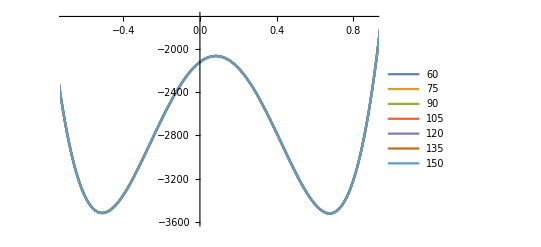

```mathematica
testPot[Λ_,phi_]=N[VrenEffMS]/.paramRules;
Plot[Evaluate[Table[Re[testPot[kk,phi]],{kk,60,150,15}]],{phi,-1,1},PlotLegends->Placed[Table[kk,{kk,60,150,15}],Right],PlotRange->{{-.7,.9},{-3600,-1700}}]
```

```mathematica
FindMinimum[testPot[100,phi],{phi,-1}]
FindMinimum[testPot[100,phi],{phi,1}]
```

{-3517.47,{phi→-0.509516}}

{-3521.98,{phi→0.676413}}

```mathematica
VrenEffMS-CWplanarSummedPerEll-VV[phi];
```

```mathematica
ClearAll[tadpoleContrib]
tadpoleContrib[phi_,Λ_]=FullSimplify[Normal@Series[D[VrenEffMS-CWplanarSummedPerEll-VV[phi]/.{Vproxy->Vpp[phi],Vfalse->Vpp[phiFalse]},{phi,1}],{Λ,Infinity,2}],Assumptions->{-1-2b phi +3 phi^2>0,Λ>0,beta>0,H>0,μ>0}]
```

1/4 beta H^2 (b-3 phi) (Λ (3+Λ)+(1+beta H^2 (1+2 b phi-3 phi^2)) Log[Λ/μ])

```mathematica
fakeBounce[chi_]=-ArcTan[chi];
```

```mathematica
bounce[chi_]=Get[StringJoin[NotebookDirectory[],"bounceJuan20DigitsExtended.wdx"]];
```

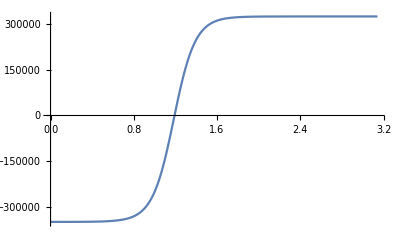

```mathematica
Plot[tadpoleContrib[bounce[chi],100]/.paramRules,{chi,0,Pi}]
```